# The Chiral Excitation Energies for 135Pr

## The symmetric and asymmetric excitation energies

```mathematica
ClearAll["Global`*"]
```

Helper functions

```mathematica
thesispath="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
export[object_,name_,format_]:=Export[StringTemplate["``/``.``"][thesispath,name, format],object/. {EdgeForm[],r_?(MemberQ[{RGBColor,Hue,CMYKColor,GrayLevel},Head[#]]&),i___}:>{EdgeForm[r],r,i}, ImageResolution->1500];
linspace[a_,b_,n_]:=Table[q,{q,a,b,(b-a)/(n-1)}];
```

Fit parameters

```mathematica
moisfit1={91,9,51};
thetadegfit1=-119;
oddspin=5.5;
spinvalues=Table[q,{q,7.5,27.5,2}];
A[mois_,k_]:=N[1/(2*#)&/@mois][[k]];
rad[theta_]:=N[theta*π/180];
j[thetadeg_,k_]:={oddspin*Cos[rad[thetadeg]],oddspin*Sin[rad[thetadeg]]}[[k]];
```

Functions

```mathematica
A21[I_,thetadeg_,mois_]:=A[mois,2]-A[mois,1]-(A[mois,2]*j[thetadeg,2])/I;
omega[I_,thetadeg_,mois_]:=(((2I+1)*A21[I,thetadeg,mois]+2A[mois,1]*j[thetadeg,1])*((2I+1)(A[mois,3]-A[mois,1])+2A[mois,1]*j[thetadeg,1])-((A[mois,3]-A[mois,1])*A21[I,thetadeg,mois]))^(1/2);
```

Excitation energies

```mathematica
Esymm[I_,thetadeg_,mois_]:=A[mois,1]*I^2+1/2(omega[I,thetadeg,mois]+omega[I,thetadeg+180,mois]);
Easymm[I_,thetadeg_,mois_]:=(2I+1)*A[mois,1]*j[thetadeg,1]-I*A[mois,2]*j[thetadeg,2]+1/2(omega[I,thetadeg,mois]-omega[I,thetadeg+180,mois]);
```

Tabular representation of the data

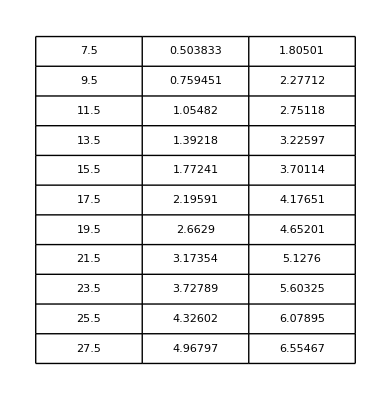

```mathematica
GraphicsGrid[Table[{spin,Esymm[spin,thetadegfit1,moisfit1],Easymm[spin,thetadegfit1,moisfit1]},{spin,spinvalues}],Frame->All]
```

Graphical representation of the data

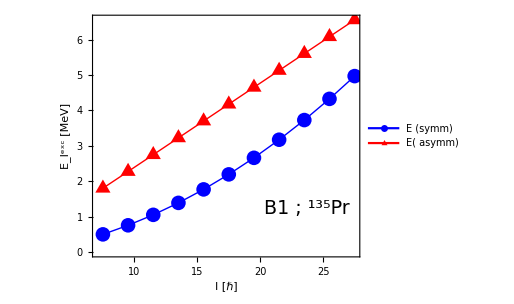

```mathematica
symmdata=Table[{spin,Esymm[spin,thetadegfit1,moisfit1]},{spin,spinvalues}];
asymmdata=Table[{spin,Easymm[spin,thetadegfit1,moisfit1]},{spin,spinvalues}];
isotope=Row[{"B1 ; ",Superscript["","135"],"Pr"}];
plot=ListLinePlot[{symmdata,asymmdata},
ImageSize->380,
AspectRatio->0.8,
Frame->True,
Axes->False,
FrameStyle->Directive[Black,Thick],
FrameLabel->{"I [ℏ]","E_I^exc [MeV]"},
PlotLegends->Placed[{"E (symm)","E( asymm)"},{0.27,0.8}],
Joined->True,
PlotStyle->{{Blue,Thick},{Red,Thick}},
PlotMarkers->{{"●", 15}, {"▲", 18}},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
Epilog->{ Inset[Style[isotope,Black,FontFamily->"Latin Modern Roman",19],Scaled[{0.8,0.2}]]}
];
Show[plot]
export[Show[plot],"chiral-excitation-energies-135Pr","pdf"];
```